# Code from the paper

```mathematica
AppendTo[$Path,NotebookDirectory[]<>"../src"];
AppendTo[$Path,NotebookDirectory[]];
<<affine.m;
```

This notebook contatins the code from all listings in the paper and code used to create the figures. The code appears in the same order as in paper. Section titles from the paper are also given.

## 3 Core datastructures

3.1 Weights

```mathematica
w=makeFiniteWeight[{1,0,3}];
v=makeFiniteWeight[{3,2,1}];
2*w+v==makeFiniteWeight[{5,2,7}]
w.v==6
```

True

True

3.2 Root systems

```mathematica
b2b4=makeFiniteRootSystem[{{1,-1,0,0},{0,1,0,0}}]
```

finiteRootSystem[2,4,{finiteWeight[4,{1,-1,0,0}],finiteWeight[4,{0,1,0,0}]}]

```mathematica
b2=makeSimpleRootSystem[B,2]
```

finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}]

```mathematica
Subscript[B, 2]==makeSimpleRootSystem[B,2]
```

True

```mathematica
b2affine=makeAffineExtension[b2]
```

affineRootSystem[2,finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}],affineWeight[2,finiteWeight[2,{-1,-1}],0,1],{affineWeight[2,finiteWeight[2,{1,-1}],0,0],affineWeight[2,finiteWeight[2,{0,1}],0,0]}]

```mathematica
Subscript[A, 1]⊕Subscript[A, 1]===finiteRootSystem[2,2,{finiteWeight[2,{1,0}],finiteWeight[2,{0,1}]}]
```

True

```mathematica
rho[b2]
```

finiteWeight[2,{3/2,1/2}]

```mathematica
weight[b2][1,2]==makeFiniteWeight[{2,1}]
```

True

```mathematica
w=weylGroupElement[b2][1,2,1];
w@makeFiniteWeight[{1,0}]==makeFiniteWeight[{-1,0}]
```

True

Computation of lexicographically minimal form for Weyl group elements can be conveniently implemented through the use of pattern-matching in Mathematica. Wilberd van der Kallen published his Mathematica rewrite rules for simple finite-dimensional and affine Lie algebras on the website http://www.staff.science.uu.nl/~kalle101/ickl/shortlex.html . Our presentation of Weyl group elements is compatible with the code of Wilberd van der Kallen . We have included A3reduce  file for this example. Other rewrite rules are available on the web.

```mathematica
<<A3reduce;
reduce[s[1,2,1,2,1,3,2,1,1]]
el=(weylGroupElement[Subscript[A, 3]]@@reduce[s[1,2,1,2,1,3,2,1,1]])@weight[Subscript[A, 3]][-1,-2,-1]
dynkinLabels[Subscript[A, 3]][el]
```

s[2,3,2]

finiteWeight[4,{-2,2,1,-1}]

{-4,1,2}

3.3 Formal elements

```mathematica
fe=makeFormalElement[{makeFiniteWeight[{1,1}],makeFiniteWeight[{0,0}]},{1,2}]*(2*Exp[makeFiniteWeight[{1,0}]]*makeFormalElement[{makeFiniteWeight[{1,1}],makeFiniteWeight[{0,0}]},{1,2}]);
fe[weights]
fe[multiplicities]
```

{finiteWeight[2,{1,0}],finiteWeight[2,{2,1}],finiteWeight[2,{3,2}]}

{8,8,2}

3.4 Modules

We need to redefine textPlot in order to set some default options to get better presentation

```mathematica
Clear[textPlot];
textPlot[m_module]:=drawPlaneProjection[1,2,character[m],{Frame->True,GridLines->Automatic,PlotRange->{{-3,3},{-3,3}}, PlotRangeClipping->True}]
```

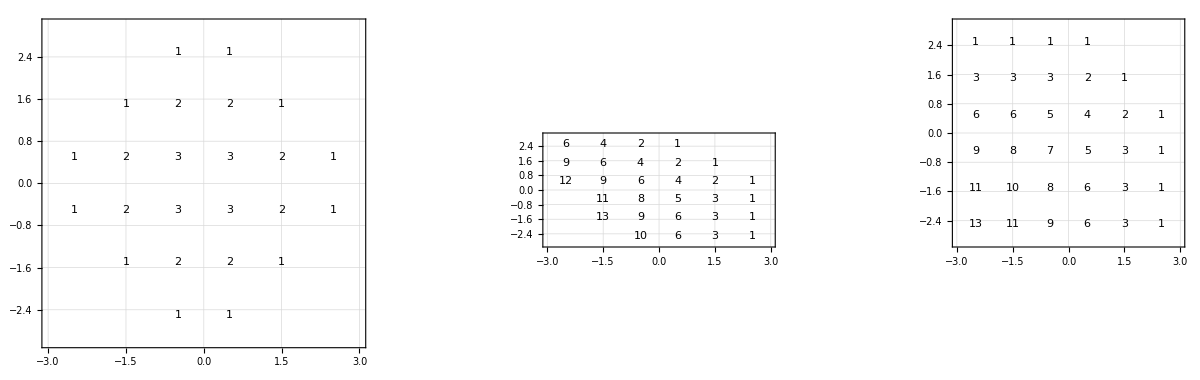

```mathematica
vm=makeVermaModule[Subscript[B, 2]][{2,1}];
pm=makeParabolicVermaModule[Subscript[B, 2]][weight[Subscript[B, 2]][2,1],{1}];
im=makeIrreducibleModule[Subscript[B, 2]][2,1];
GraphicsRow[textPlot/@{im,vm,pm}]
```

This code can be used to get pdf file in the paper :

```mathematica
Export["irrep-verma-pverma.pdf",GraphicsRow[textPlot/@{im,vm,pm}]]
```

irrep-verma-pverma.pdf

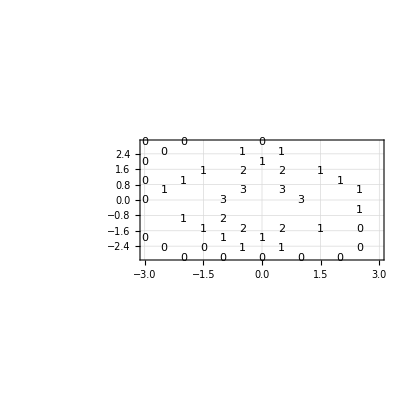

```mathematica
im1=makeIrreducibleModule[Subscript[B, 2]][weight[Subscript[B, 2]][2,1]];
im2=makeIrreducibleModule[Subscript[B, 2]][weight[Subscript[B, 2]][1,2]];
textPlot[im1⊕ im2]
```

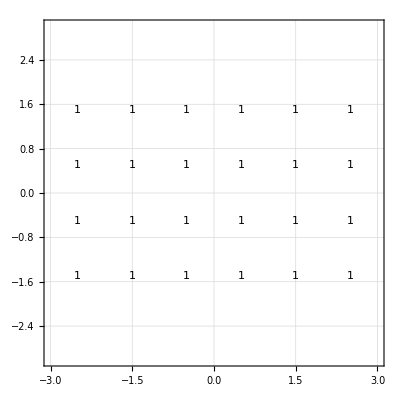

```mathematica
textPlot[makeIrreducibleModule[Subscript[A, 1]][5]⊗ makeIrreducibleModule[Subscript[A, 1]][3]]
```

## 4 Computational algorightms

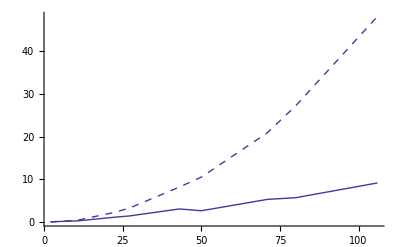

```mathematica
tt1=Table[freudenthalMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
tt2=Table[racahMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
Table[freudenthalMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
Table[racahMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
Show[ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt1,{Joined-> True,PlotStyle->Dashed}], ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt2,{Joined-> True,PlotStyle->Thick}]]
```

To get timing.pdf file in the paper use the code :

```mathematica
Export["timing.pdf",Show[ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt1,{Joined-> True,PlotStyle->Dashed}], ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt2,{Joined-> True,PlotStyle->Thick}]]]
```

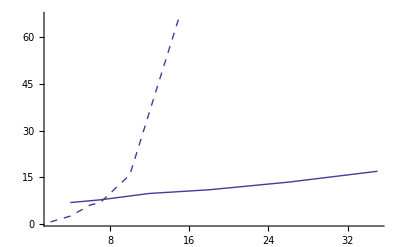

```mathematica
tt3=Timing[simpleBranching[Subscript[B, 4],parabolicSubalgebra[Subscript[B, 4]][2,3,4]][weight[Subscript[B, 4]][Sequence@@#]]]&/@ Flatten[IntegerPartitions[#,{4},Range[0,#]]&/@Range[3],1];
tt4=Timing[ourBranching[makeIrreducibleModule[Subscript[B, 4]][Sequence@@#],parabolicSubalgebra[Subscript[B, 4]][2,3,4]]]&/@ 
Table[{i,i,0,0},{i,0,5}];
gr1=Show[ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt3,{Joined->True, PlotStyle->Dashed}],
ListPlot[{Length[#[[2]][weights]],#[[1]]}&/@tt4,{Joined->True, PlotStyle->Thick}]]
```

To get branching-timing.pdf file in the paper use the code :

```mathematica
Export["branching-timing.pdf",gr1]
```

## 5. Examples

5.1 Tensor product decompositon for finite - dimensional Lie algebras

```mathematica
fm=makeIrreducibleModule[Subscript[B, 2]][1,0];
tp=((fm⊗fm)⊗ fm)⊗fm;
subs=makeFiniteRootSystem[{1/4*{1,-1,1,-1,1,-1,1,-1},1/4*{0,1,0,1,0,1,0,1}}];
bc=branching[tp,subs];
{bc[#],dynkinLabels[subs][#]}&/@bc[weights]
```

{{1,{4,0}},{3,{2,2}},{0,{3,0}},{2,{0,4}},{3,{1,2}},{6,{2,0}},{6,{0,2}},{1,{1,0}},{3,{0,0}}}

5.2 Branching and parabolic Verma modules

To produce nice pictures of G2 - modules we need to construct orthogonal basis in G2 weight space. We orthogonalize basis of simple roots :

```mathematica
α=simpleRoots[Subscript[G, 2]];
ort={α[[1]],α[[2]]-α[[1]]*(α[[2]].α[[1]])/(α[[1]].α[[1]])};
ort=2*(1/(#.#)^(1/2))*#&/@ort
```

{finiteWeight[3,{√2,-√2,0}],finiteWeight[3,{-√(2/3),-√(2/3),2 √(2/3)}]}

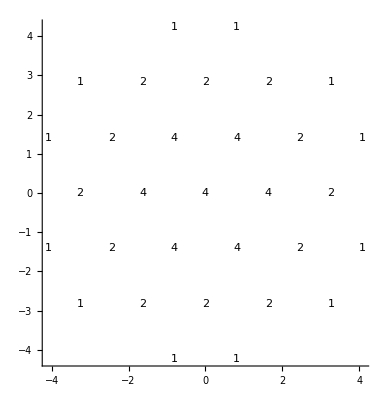

```mathematica
ch=character[makeIrreducibleModule[Subscript[G, 2]][1,1]];
Graphics[Text[ch[#],{#.ort[[1]],#.ort[[2]]}]&/@ch[weights],{Axes->True}]
```

We use following function to plot characters of G2 - modules. Note that we hide multiplicities greater than 100.

```mathematica
gr[ch1_]:=Graphics[Text[If[ch1[#]<100,ch1[#],".."],{#.ort[[1]],#.ort[[2]]}]&/@ch1[weights],{Frame->True,GridLines->{{-8,-4,0,4},{-8,-4,0,4}},GridLinesStyle->Directive[Gray,Dashed],PlotRangeClipping->True,PlotRange->{{-12,6},{-12,5}}}];
```

To get the plot of Figure 4 we should plot characters of modules appearing in the decomposition of irreducible module.

```mathematica
ch1=formalOrbit[Subscript[G, 2]][weight[Subscript[G, 2]][1,1]+rho[Subscript[G, 2]]];graphs=gr[character[makeParabolicVermaModule[Subscript[G, 2]][#-rho[Subscript[G, 2]],{2},20]]]&/@Select[ch1[weights],#.α[[2]]≥0&];
```

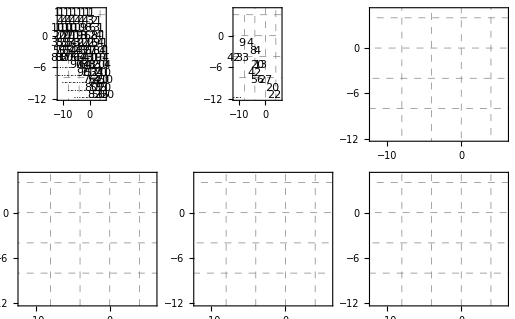

```mathematica
GraphicsGrid[{graphs[[{1,3,5}]],graphs[[{2,4,6}]]}]
```

To export the graph as pdf file we can use the code

```mathematica
Export["G2-pverma.pdf",GraphicsGrid[{graphs[[{1,3,5}]],graphs[[{2,4,6}]]}]]
```

5.3 String functions of affine Lie algebras and CFT models

```mathematica
stringFunctions[OverHat[Subscript[A, 2]],{1,1,2}]
```

{{{0,3,1},2 q+12 q^2+49 q^3+166 q^4+494 q^5+1340 q^6+3387 q^7+8086 q^8+18415 q^9+40302 q^10},{{2,2,0},1+8 q+35 q^2+124 q^3+379 q^4+1052 q^5+2700 q^6+6536 q^7+15047 q^8+33248 q^9+70877 q^10},{{3,0,1},2+12 q+49 q^2+166 q^3+494 q^4+1340 q^5+3387 q^6+8086 q^7+18415 q^8+40302 q^9+85226 q^10},{{0,0,4},2 q+10 q^2+40 q^3+133 q^4+398 q^5+1084 q^6+2760 q^7+6632 q^8+15214 q^9+33508 q^10},{{1,1,2},1+6 q+27 q^2+96 q^3+298 q^4+836 q^5+2173 q^6+5310 q^7+12341 q^8+27486 q^9+59029 q^10}}

```mathematica
stringFunctions[OverHat[Subscript[G, 2]],{1,1,0}]
```

{{{1,1,0},1+7 q+32 q^2+117 q^3+370 q^4+1055 q^5+2780 q^6+6880 q^7+16172 q^8+36402 q^9+78954 q^10},{{0,0,1},3 q+18 q^2+73 q^3+247 q^4+736 q^5+2000 q^6+5070 q^7+12146 q^8+27766 q^9+61015 q^10},{{0,2,0},3 q+15 q^2+63 q^3+210 q^4+633 q^5+1725 q^6+4407 q^7+10605 q^8+24390 q^9+53832 q^10},{{2,0,0},1+8 q+37 q^2+138 q^3+431 q^4+1227 q^5+3208 q^6+7901 q^7+18458 q^8+41358 q^9+89261 q^10}}

5.4 Branching functions and coset models of conformal field theory

```mathematica
branchingFunctions[OverHat[Subscript[B, 2]],makeAffineExtension[makeFiniteRootSystem[{{1,1}}]],{1,1,1}]
```

{{{1,2},2+14 q+54 q^2+168 q^3+462 q^4+1148 q^5+2656 q^6+5812 q^7+12130 q^8+24358 q^9+47328 q^10},{{3,0},2+14 q+52 q^2+154 q^3+410 q^4+994 q^5+2248 q^6+4832 q^7+9934 q^8+19680 q^9+37802 q^10},{{0,3},4 q+20 q^2+68 q^3+200 q^4+516 q^5+1224 q^6+2736 q^7+5808 q^8+11820 q^9+23236 q^10},{{2,1},4+20 q+72 q^2+220 q^3+584 q^4+1424 q^5+3248 q^6+7012 q^7+14488 q^8+28844 q^9+55616 q^10}}